#### Problem description

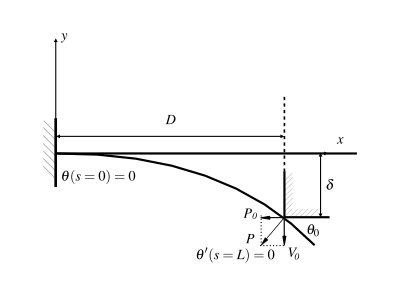

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d t^2)-P_1 sin(θ)+ P_2 cos(θ)=0

where 0≤t≤S/2 is the arc length coordinate, θ is the angle of deflection (in radians) at point t, P_1 (positive when pointing to right) and P_2 (positive when pointing downward) are the horizontal and vertical forces at the left end of the beam, respectively.

Let ξ=t/(S/2), then the equation becomes

(4E I)/S^2 (d^2 θ)/dξ^2-P_1 sin(θ)+ P_2 cos(θ)=0

Note that

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)
-P_2=P_n cos(θ_0)+μ P_n sin(θ_0)

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)=P_n( sin(θ_0)-μ cos(θ_0))
P_2=-(P_n cos(θ_0)+μ P_n sin(θ_0))=-P_n(cos(θ_0)+μ sin(θ_0))

where θ_0=θ(ξ=0)>0, P_n>0 is the magnitude of the reaction force. Thus

(4E I)/(P_n S^2) (d^2 θ)/(d ξ^2)-( sin(θ_0)-μ cos(θ_0))sin(θ)- (cos(θ_0)+μ sin(θ_0))cos(θ)=0
 (d^2 θ)/dξ^2-(P_n S^2)/(4E I) (cos(θ_0-θ)+μ sin(θ_0-θ))=0
 (d^2 θ)/dξ^2-(P_n S^2)/(4E I) (cos(θ-θ_0)-μ sin(θ-θ_0))=0

Let k=(P_n S^2)/(4E I), g=θ-θ_0. Note that

g(ξ=0)=θ(ξ=0)-θ_0=0
g(ξ=1)=θ(ξ=1)-θ_0=-θ_0
g'(ξ=0)=θ'(ξ=0)=0

The simplified governing equation and boundary conditions are as follows

(d^2 g)/dξ^2-k (cos(g)-μ sin(g))=0
g(0)=0
g'(0)=0
g(1)=-θ_0

It seems like that the sign of θ is flipped. Because we are working in a Left-hand Cartesian coordinate system.

θ_0=-(-g(1))
θ=-(g-g(1))
L=S∫_0^1 cos(θ(ξ)) dξ
w_0=S/2∫_0^1 sin(θ(ξ)) dξ
(P_n L^2)/(4E I)=(P_n S^2)/(4E I)(L/S)^2=k (L/S)^2=(k(∫_0^1 cos(θ) dξ))^2
(2 w_0)/L=(∫_0^1 sin(θ) dξ)/(∫_0^1 cos(θ) dξ)

### Force-deflection relations

θ_0=-(-g(1))
θ=-(g-g(1))
(P_n L^2)/(4E I)=(k(∫_0^1 cos(θ) dξ))^2
-P_2=P_n cos(θ_0)+μ P_n sin(θ_0)
F=-2 P_2=2(P_n cos(θ_0)+μ P_n sin(θ_0))
F=2P_n( cos(θ_0)+μ sin(θ_0))
(F L^2)/(4E I)=(P_n L^2)/(4E I)F/P_n=(P_n L^2)/(4E I)2( cos(θ_0)+μ sin(θ_0))
(F L^2)/(4E I)=2(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
(F L^2)/(E I)=8(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
F̂=(F L^2)/(E I)=8(k(∫_0^1 cos(θ) dξ))^2( cos(θ_0)+μ sin(θ_0))
OverHat[w_0]=w_0/L=(∫_0^1 sin(θ) dξ)/(2∫_0^1 cos(θ) dξ)

### Contour plot

```mathematica
SolutionVector2=Table[ParallelTable[solg=NDSolve[{g''[ξ]-k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
θ[ξ_]=-(g[ξ]-g[1])/.solg[[1]];
θ0=g[ξ]/.solg[[1]]/.ξ->1;
If[θ0<π/2,
IntSinθ=NIntegrate[Sin[θ[ξ]],{ξ,0,1}];
IntCosθ=NIntegrate[Cos[θ[ξ]],{ξ,0,1}];
w=IntSinθ/(2IntCosθ);
F=8k IntCosθ^2( Cos[θ0]+μ  Sin[θ0]);
{w,F,k,θ0,1/IntCosθ,μ}],{k,0.001,5,0.002}],{μ,0.0,1.0,0.002}];
```

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]];
Save["SolutionVector2_Feb3",SolutionVector2]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"SolutionVector2_Feb3"
```

{{{0.000166667 Get,0.008 Get,0.001 Get,0.0005 Get,1. Get,0.},{0.0005 Get,0.0239999 Get,0.003 Get,0.0015 Get,1. Get,0.},{0.000833334 Get,0.0399997 Get,0.005 Get,0.0025 Get,1. Get,0.},2494,Get Null,Get Null,Get Null},499,{{0.00016665 Get,4,1. Get},2498,{1}}}
 |  |  |  |

```mathematica
SolutionVector2//Dimensions
```

{501,2500}

```mathematica
SolutionVector2/.Null->Nothing
```

$Aborted[]

```mathematica
Num =Length@Range[0.0,1.0,0.002];
colorlist =ColorData["Rainbow"]/@((Range@Num-1)/(Num-1))
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.466280736, 0.10904804800000001, 0.531414496],RGBColor[0.461149472, 0.109330096, 0.535812992],RGBColor[0.456018208, 0.10961214400000001, 0.5402114880000001],RGBColor[0.450886944, 0.109894192, 0.544609984],RGBColor[0.44575568, 0.11017624000000001, 0.54900848],RGBColor[0.440624416, 0.110458288, 0.553406976],RGBColor[0.435493152, 0.11074033600000001, 0.5578054720000001],RGBColor[0.43036188799999997, 0.111022384, 0.562203968],RGBColor[0.425230624, 0.11130443200000001, 0.566602464],RGBColor[0.42009936, 0.11158648, 0.57100096],RGBColor[0.414968096, 0.11186852800000001, 0.575399456],RGBColor[0.409836832, 0.112150576, 0.5797979520000001],RGBColor[0.404705568, 0.11243262400000001, 0.584196448],RGBColor[0.399574304, 0.112714672, 0.588594944],RGBColor[0.39444304, 0.11299672000000001, 0.59299344],RGBColor[0.389311776, 0.113278768, 0.597391936],RGBColor[0.384180512, 0.11356081600000001, 0.601790432],RGBColor[0.379049248, 0.113842864, 0.606188928],RGBColor[0.373917984, 0.11412491200000001, 0.610587424],RGBColor[0.36878672, 0.11440696, 0.61498592],RGBColor[0.363655456, 0.11468900800000001, 0.619384416],RGBColor[0.358524192, 0.114971056, 0.623782912],RGBColor[0.353392928, 0.11525310400000001, 0.628181408],RGBColor[0.348261664, 0.115535152, 0.632579904],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.337999136, 0.116099248, 0.641376896],RGBColor[0.332867872, 0.11638129600000001, 0.645775392],RGBColor[0.32773660800000004, 0.116663344, 0.650173888],RGBColor[0.32260534399999996, 0.11694539200000001, 0.654572384],RGBColor[0.31747408, 0.11722744, 0.65897088],RGBColor[0.312342816, 0.11750948800000001, 0.663369376],RGBColor[0.309612032, 0.12016734400000001, 0.666981392],RGBColor[0.307681408, 0.123617136, 0.670331248],RGBColor[0.305750784, 0.127066928, 0.6736811039999999],RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.301889536, 0.133966512, 0.680380816],RGBColor[0.299958912, 0.137416304, 0.6837306719999999],RGBColor[0.29802828800000003, 0.140866096, 0.687080528],RGBColor[0.296097664, 0.144315888, 0.690430384],RGBColor[0.29416704, 0.14776568, 0.6937802399999999],RGBColor[0.292236416, 0.15121547200000002, 0.697130096],RGBColor[0.290305792, 0.154665264, 0.700479952],RGBColor[0.288375168, 0.158115056, 0.703829808],RGBColor[0.286444544, 0.161564848, 0.707179664],RGBColor[0.28451392, 0.16501464, 0.7105295199999999],RGBColor[0.282583296, 0.168464432, 0.713879376],RGBColor[0.280652672, 0.171914224, 0.717229232],RGBColor[0.278722048, 0.175364016, 0.7205790879999999],RGBColor[0.276791424, 0.178813808, 0.723928944],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.272930176, 0.185713392, 0.7306286559999999],RGBColor[0.27099955200000003, 0.189163184, 0.733978512],RGBColor[0.269068928, 0.192612976, 0.737328368],RGBColor[0.267138304, 0.196062768, 0.7406782239999999],RGBColor[0.26520768, 0.19951256, 0.74402808],RGBColor[0.263277056, 0.202962352, 0.7473779359999999],RGBColor[0.261346432, 0.206412144, 0.750727792],RGBColor[0.259415808, 0.209861936, 0.754077648],RGBColor[0.257485184, 0.213311728, 0.7574275039999999],RGBColor[0.25555456, 0.21676152, 0.76077736],RGBColor[0.253623936, 0.220211312, 0.7641272159999999],RGBColor[0.251693312, 0.223661104, 0.7674770719999999],RGBColor[0.250621632, 0.227559696, 0.7699029119999999],RGBColor[0.250408896, 0.231907088, 0.7714047359999999],RGBColor[0.25019616, 0.23625448, 0.7729065599999999],RGBColor[0.249983424, 0.240601872, 0.774408384],RGBColor[0.249770688, 0.244949264, 0.775910208],RGBColor[0.249557952, 0.249296656, 0.777412032],RGBColor[0.249345216, 0.253644048, 0.778913856],RGBColor[0.24913248, 0.25799144, 0.78041568],RGBColor[0.248919744, 0.262338832, 0.7819175039999999],RGBColor[0.248707008, 0.266686224, 0.783419328],RGBColor[0.248494272, 0.271033616, 0.784921152],RGBColor[0.248281536, 0.275381008, 0.786422976],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.247856064, 0.284075792, 0.789426624],RGBColor[0.247643328, 0.288423184, 0.790928448],RGBColor[0.247430592, 0.292770576, 0.7924302719999999],RGBColor[0.24721785599999999, 0.297117968, 0.793932096],RGBColor[0.24700512, 0.30146536, 0.79543392],RGBColor[0.246792384, 0.305812752, 0.796935744],RGBColor[0.24657964799999998, 0.310160144, 0.798437568],RGBColor[0.246366912, 0.31450753600000003, 0.799939392],RGBColor[0.246154176, 0.318854928, 0.801441216],RGBColor[0.24594143999999998, 0.32320232, 0.80294304],RGBColor[0.245728704, 0.327549712, 0.804444864],RGBColor[0.245515968, 0.331897104, 0.805946688],RGBColor[0.24530323199999998, 0.336244496, 0.807448512],RGBColor[0.245090496, 0.340591888, 0.808950336],RGBColor[0.24487776, 0.34493928, 0.81045216],RGBColor[0.24466502399999998, 0.349286672, 0.8119539840000001],RGBColor[0.244452288, 0.35363406399999997, 0.8134558080000001],RGBColor[0.244239552, 0.357981456, 0.814957632],RGBColor[0.244256336, 0.362245376, 0.81597556],RGBColor[0.24496168, 0.36625888, 0.8155418],RGBColor[0.24566702399999998, 0.370272384, 0.81510804],RGBColor[0.246372368, 0.374285888, 0.8146742800000001],RGBColor[0.247077712, 0.378299392, 0.81424052],RGBColor[0.247783056, 0.382312896, 0.8138067600000001],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.249193744, 0.390339904, 0.8129392400000001],RGBColor[0.249899088, 0.394353408, 0.81250548],RGBColor[0.250604432, 0.398366912, 0.81207172],RGBColor[0.251309776, 0.402380416, 0.81163796],RGBColor[0.25201512, 0.40639392, 0.8112042],RGBColor[0.25272046400000003, 0.410407424, 0.8107704400000001],RGBColor[0.25342580800000003, 0.41442092799999997, 0.81033668],RGBColor[0.254131152, 0.418434432, 0.8099029200000001],RGBColor[0.254836496, 0.42244793599999997, 0.80946916],RGBColor[0.25554184, 0.42646143999999997, 0.8090354000000001],RGBColor[0.256247184, 0.43047494399999997, 0.80860164],RGBColor[0.256952528, 0.43448844799999997, 0.8081678800000001],RGBColor[0.257657872, 0.438501952, 0.80773412],RGBColor[0.258363216, 0.442515456, 0.80730036],RGBColor[0.25906856, 0.44652896, 0.8068666],RGBColor[0.259773904, 0.450542464, 0.80643284],RGBColor[0.260479248, 0.454555968, 0.8059990800000001],RGBColor[0.261184592, 0.458569472, 0.80556532],RGBColor[0.26188993600000005, 0.462582976, 0.8051315600000001],RGBColor[0.26259528000000004, 0.46659648, 0.8046978],RGBColor[0.26330062400000004, 0.470609984, 0.8042640400000001],RGBColor[0.26400596800000004, 0.474623488, 0.80383028],RGBColor[0.26471131200000003, 0.478636992, 0.8033965200000001],RGBColor[0.26541665600000003, 0.482650496, 0.80296276],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.267395504, 0.489829152, 0.800517384],RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],RGBColor[0.269942512, 0.496159456, 0.7964941520000001],RGBColor[0.271216016, 0.499324608, 0.7944825360000001],RGBColor[0.27248952000000004, 0.50248976, 0.7924709200000001],RGBColor[0.273763024, 0.505654912, 0.7904593040000001],RGBColor[0.275036528, 0.508820064, 0.7884476880000001],RGBColor[0.27631003200000004, 0.511985216, 0.7864360720000001],RGBColor[0.277583536, 0.515150368, 0.784424456],RGBColor[0.27885704, 0.51831552, 0.78241284],RGBColor[0.28013054400000004, 0.5214806719999999, 0.780401224],RGBColor[0.281404048, 0.5246458239999999, 0.778389608],RGBColor[0.282677552, 0.5278109759999999, 0.776377992],RGBColor[0.28395105600000003, 0.5309761279999999, 0.774366376],RGBColor[0.28522456, 0.5341412799999999, 0.77235476],RGBColor[0.286498064, 0.537306432, 0.770343144],RGBColor[0.28777156800000003, 0.540471584, 0.768331528],RGBColor[0.289045072, 0.543636736, 0.766319912],RGBColor[0.290318576, 0.546801888, 0.764308296],RGBColor[0.29159208000000003, 0.54996704, 0.7622966800000001],RGBColor[0.292865584, 0.553132192, 0.7602850640000001],RGBColor[0.294139088, 0.556297344, 0.7582734480000001],RGBColor[0.29541259200000003, 0.559462496, 0.7562618320000001],RGBColor[0.296686096, 0.562627648, 0.7542502160000001],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.299233104, 0.568957952, 0.7502269840000001],RGBColor[0.300506608, 0.572123104, 0.7482153680000001],RGBColor[0.301780112, 0.575288256, 0.746203752],RGBColor[0.303053616, 0.578453408, 0.744192136],RGBColor[0.30432712, 0.5816185599999999, 0.74218052],RGBColor[0.305600624, 0.5847837119999999, 0.740168904],RGBColor[0.307228464, 0.587259416, 0.737410624],RGBColor[0.308974416, 0.589505304, 0.734403456],RGBColor[0.310720368, 0.5917511919999999, 0.731396288],RGBColor[0.31246632, 0.59399708, 0.72838912],RGBColor[0.314212272, 0.596242968, 0.725381952],RGBColor[0.315958224, 0.598488856, 0.722374784],RGBColor[0.317704176, 0.6007347439999999, 0.7193676160000001],RGBColor[0.319450128, 0.602980632, 0.7163604480000001],RGBColor[0.32119608, 0.60522652, 0.7133532800000001],RGBColor[0.322942032, 0.607472408, 0.7103461120000001],RGBColor[0.324687984, 0.6097182959999999, 0.7073389440000001],RGBColor[0.32643393600000004, 0.611964184, 0.7043317760000001],RGBColor[0.32817988800000003, 0.614210072, 0.7013246080000001],RGBColor[0.32992584, 0.6164559599999999, 0.6983174400000001],RGBColor[0.331671792, 0.6187018479999999, 0.6953102720000001],RGBColor[0.333417744, 0.620947736, 0.6923031040000001],RGBColor[0.335163696, 0.623193624, 0.689295936],RGBColor[0.336909648, 0.6254395119999999, 0.686288768],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.340401552, 0.629931288, 0.680274432],RGBColor[0.34214750400000005, 0.632177176, 0.677267264],RGBColor[0.343893456, 0.6344230639999999, 0.674260096],RGBColor[0.34563940800000004, 0.636668952, 0.671252928],RGBColor[0.34738536000000003, 0.63891484, 0.66824576],RGBColor[0.349131312, 0.641160728, 0.665238592],RGBColor[0.350877264, 0.6434066159999999, 0.662231424],RGBColor[0.352623216, 0.645652504, 0.659224256],RGBColor[0.354369168, 0.647898392, 0.656217088],RGBColor[0.35611512, 0.65014428, 0.65320992],RGBColor[0.357861072, 0.6523901679999999, 0.650202752],RGBColor[0.359607024, 0.654636056, 0.6471955840000001],RGBColor[0.361589792, 0.65649644, 0.644006064],RGBColor[0.363809376, 0.65797132, 0.640634192],RGBColor[0.36602896, 0.6594462, 0.63726232],RGBColor[0.368248544, 0.6609210799999999, 0.633890448],RGBColor[0.370468128, 0.66239596, 0.630518576],RGBColor[0.372687712, 0.66387084, 0.627146704],RGBColor[0.374907296, 0.6653457199999999, 0.6237748320000001],RGBColor[0.37712688, 0.6668206, 0.6204029600000001],RGBColor[0.379346464, 0.6682954799999999, 0.6170310880000001],RGBColor[0.381566048, 0.66977036, 0.6136592160000001],RGBColor[0.38378563200000004, 0.67124524, 0.6102873440000001],RGBColor[0.38600521600000004, 0.6727201199999999, 0.6069154720000001],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.39044438400000003, 0.67566988, 0.6001717280000001],RGBColor[0.39266396800000003, 0.67714476, 0.5967998560000001],RGBColor[0.394883552, 0.67861964, 0.5934279840000001],RGBColor[0.397103136, 0.6800945199999999, 0.5900561120000001],RGBColor[0.39932272, 0.6815694, 0.5866842400000001],RGBColor[0.401542304, 0.68304428, 0.5833123680000001],RGBColor[0.403761888, 0.68451916, 0.5799404960000001],RGBColor[0.405981472, 0.68599404, 0.5765686240000001],RGBColor[0.408201056, 0.6874689199999999, 0.5731967520000001],RGBColor[0.41042064, 0.6889438, 0.5698248800000001],RGBColor[0.412640224, 0.69041868, 0.5664530080000001],RGBColor[0.414859808, 0.6918935599999999, 0.5630811360000001],RGBColor[0.417079392, 0.69336844, 0.5597092640000001],RGBColor[0.419298976, 0.6948433199999999, 0.5563373920000001],RGBColor[0.42151856, 0.6963182, 0.5529655200000001],RGBColor[0.423738144, 0.69779308, 0.5495936480000001],RGBColor[0.425957728, 0.6992679599999999, 0.5462217760000001],RGBColor[0.428177312, 0.70074284, 0.5428499040000001],RGBColor[0.4305106, 0.702073568, 0.5395238880000001],RGBColor[0.433185, 0.7029718399999999, 0.53633544],RGBColor[0.4358594, 0.7038701119999999, 0.533146992],RGBColor[0.43853380000000003, 0.704768384, 0.5299585440000001],RGBColor[0.4412082, 0.705666656, 0.526770096],RGBColor[0.4438826, 0.7065649279999999, 0.5235816480000001],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.4492314, 0.708361472, 0.517204752],RGBColor[0.4519058, 0.7092597439999999, 0.5140163040000001],RGBColor[0.4545802, 0.710158016, 0.510827856],RGBColor[0.4572546, 0.711056288, 0.5076394080000001],RGBColor[0.45992900000000003, 0.71195456, 0.50445096],RGBColor[0.4626034, 0.7128528319999999, 0.501262512],RGBColor[0.4652778, 0.713751104, 0.49807406400000004],RGBColor[0.4679522, 0.714649376, 0.49488561600000003],RGBColor[0.4706266, 0.7155476479999999, 0.491697168],RGBColor[0.473301, 0.71644592, 0.48850872],RGBColor[0.4759754, 0.717344192, 0.48532027200000005],RGBColor[0.4786498, 0.718242464, 0.48213182400000004],RGBColor[0.4813242, 0.719140736, 0.47894337600000003],RGBColor[0.4839986, 0.720039008, 0.475754928],RGBColor[0.486673, 0.72093728, 0.47256648],RGBColor[0.4893474, 0.7218355519999999, 0.46937803200000006],RGBColor[0.4920218, 0.722733824, 0.46618958400000005],RGBColor[0.49469620000000003, 0.723632096, 0.46300113600000004],RGBColor[0.4973706, 0.724530368, 0.459812688],RGBColor[0.500045, 0.72542864, 0.45662424],RGBColor[0.5027194, 0.726326912, 0.453435792],RGBColor[0.5053938, 0.727225184, 0.450247344],RGBColor[0.5080682, 0.7281234560000001, 0.44705889600000004],RGBColor[0.5107426, 0.729021728, 0.44387044800000003],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.516432488, 0.730361536, 0.43805499200000003],RGBColor[0.519447976, 0.730803072, 0.43542798400000005],RGBColor[0.522463464, 0.731244608, 0.432800976],RGBColor[0.525478952, 0.731686144, 0.430173968],RGBColor[0.52849444, 0.7321276800000001, 0.42754696000000003],RGBColor[0.531509928, 0.732569216, 0.424919952],RGBColor[0.534525416, 0.733010752, 0.422292944],RGBColor[0.537540904, 0.733452288, 0.419665936],RGBColor[0.540556392, 0.733893824, 0.41703892800000003],RGBColor[0.54357188, 0.73433536, 0.41441192000000004],RGBColor[0.5465873680000001, 0.734776896, 0.411784912],RGBColor[0.549602856, 0.735218432, 0.409157904],RGBColor[0.552618344, 0.735659968, 0.40653089600000003],RGBColor[0.555633832, 0.736101504, 0.403903888],RGBColor[0.55864932, 0.73654304, 0.40127688],RGBColor[0.5616648080000001, 0.736984576, 0.398649872],RGBColor[0.564680296, 0.737426112, 0.39602286400000003],RGBColor[0.567695784, 0.737867648, 0.39339585600000004],RGBColor[0.570711272, 0.738309184, 0.390768848],RGBColor[0.57372676, 0.73875072, 0.38814184],RGBColor[0.5767422480000001, 0.739192256, 0.38551483200000003],RGBColor[0.579757736, 0.739633792, 0.38288782400000004],RGBColor[0.5827732240000001, 0.740075328, 0.380260816],RGBColor[0.585788712, 0.7405168639999999, 0.377633808],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.5918196880000001, 0.741399936, 0.37237979200000004],RGBColor[0.594835176, 0.741841472, 0.369752784],RGBColor[0.5978506640000001, 0.742283008, 0.367125776],RGBColor[0.600866152, 0.742724544, 0.36449876800000003],RGBColor[0.60388164, 0.74316608, 0.36187176],RGBColor[0.6068971280000001, 0.743607616, 0.359244752],RGBColor[0.609988288, 0.743690952, 0.35716189600000003],RGBColor[0.6131046720000001, 0.743654888, 0.355260424],RGBColor[0.6162210560000001, 0.743618824, 0.353358952],RGBColor[0.61933744, 0.74358276, 0.35145748000000004],RGBColor[0.622453824, 0.743546696, 0.34955600800000003],RGBColor[0.6255702080000001, 0.743510632, 0.347654536],RGBColor[0.6286865920000001, 0.743474568, 0.345753064],RGBColor[0.631802976, 0.743438504, 0.34385159200000004],RGBColor[0.63491936, 0.74340244, 0.34195012],RGBColor[0.6380357440000001, 0.743366376, 0.340048648],RGBColor[0.6411521280000001, 0.743330312, 0.338147176],RGBColor[0.644268512, 0.743294248, 0.33624570400000003],RGBColor[0.647384896, 0.743258184, 0.334344232],RGBColor[0.6505012800000001, 0.74322212, 0.33244276],RGBColor[0.6536176640000001, 0.743186056, 0.33054128800000004],RGBColor[0.656734048, 0.743149992, 0.32863981600000003],RGBColor[0.659850432, 0.743113928, 0.326738344],RGBColor[0.6629668160000001, 0.743077864, 0.324836872],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.669199584, 0.743005736, 0.321033928],RGBColor[0.672315968, 0.742969672, 0.319132456],RGBColor[0.6754323520000001, 0.742933608, 0.31723098400000005],RGBColor[0.6785487360000001, 0.742897544, 0.31532951200000003],RGBColor[0.68166512, 0.74286148, 0.31342804],RGBColor[0.684781504, 0.742825416, 0.311526568],RGBColor[0.6878978880000001, 0.742789352, 0.309625096],RGBColor[0.6910142720000001, 0.742753288, 0.30772362400000003],RGBColor[0.694130656, 0.742717224, 0.305822152],RGBColor[0.69724704, 0.74268116, 0.30392068],RGBColor[0.7003634240000001, 0.742645096, 0.30201920800000004],RGBColor[0.7034798080000001, 0.742609032, 0.300117736],RGBColor[0.7064701760000001, 0.742248072, 0.29855359200000003],RGBColor[0.7093345280000001, 0.741562216, 0.297326776],RGBColor[0.7121988800000001, 0.74087636, 0.29609996],RGBColor[0.715063232, 0.740190504, 0.29487314400000003],RGBColor[0.717927584, 0.739504648, 0.293646328],RGBColor[0.720791936, 0.738818792, 0.292419512],RGBColor[0.723656288, 0.738132936, 0.29119269600000003],RGBColor[0.72652064, 0.73744708, 0.28996588],RGBColor[0.7293849920000001, 0.736761224, 0.288739064],RGBColor[0.732249344, 0.736075368, 0.287512248],RGBColor[0.735113696, 0.735389512, 0.286285432],RGBColor[0.737978048, 0.734703656, 0.285058616],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.743706752, 0.733331944, 0.282604984],RGBColor[0.746571104, 0.732646088, 0.281378168],RGBColor[0.749435456, 0.7319602319999999, 0.280151352],RGBColor[0.752299808, 0.731274376, 0.278924536],RGBColor[0.75516416, 0.73058852, 0.27769772],RGBColor[0.758028512, 0.729902664, 0.276470904],RGBColor[0.760892864, 0.729216808, 0.275244088],RGBColor[0.763757216, 0.728530952, 0.274017272],RGBColor[0.7666215679999999, 0.727845096, 0.272790456],RGBColor[0.7694859199999999, 0.72715924, 0.27156364],RGBColor[0.772350272, 0.7264733839999999, 0.270336824],RGBColor[0.775214624, 0.725787528, 0.26911000799999996],RGBColor[0.778078976, 0.725101672, 0.267883192],RGBColor[0.780943328, 0.7244158159999999, 0.266656376],RGBColor[0.78380768, 0.72372996, 0.26542955999999995],RGBColor[0.786672032, 0.723044104, 0.264202744],RGBColor[0.7895363839999999, 0.7223582479999999, 0.26297592799999997],RGBColor[0.7924007359999999, 0.721672392, 0.26174911199999995],RGBColor[0.795100704, 0.720754904, 0.26063487999999996],RGBColor[0.7973075199999999, 0.71914252, 0.2598584],RGBColor[0.799514336, 0.7175301359999999, 0.25908191999999997],RGBColor[0.8017211519999999, 0.715917752, 0.25830544],RGBColor[0.803927968, 0.714305368, 0.25752896],RGBColor[0.8061347839999999, 0.7126929839999999, 0.25675248],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8105484159999999, 0.709468216, 0.25519951999999996],RGBColor[0.812755232, 0.707855832, 0.25442304],RGBColor[0.8149620479999999, 0.7062434479999999, 0.25364655999999997],RGBColor[0.817168864, 0.704631064, 0.25287008],RGBColor[0.8193756799999999, 0.70301868, 0.2520936],RGBColor[0.821582496, 0.7014062959999999, 0.25131712],RGBColor[0.8237893119999999, 0.699793912, 0.25054064],RGBColor[0.825996128, 0.698181528, 0.24976415999999999],RGBColor[0.8282029439999999, 0.696569144, 0.24898768],RGBColor[0.83040976, 0.69495676, 0.2482112],RGBColor[0.8326165759999999, 0.693344376, 0.24743472],RGBColor[0.8348233919999999, 0.691731992, 0.24665824],RGBColor[0.8370302079999999, 0.6901196079999999, 0.24588175999999998],RGBColor[0.839237024, 0.688507224, 0.24510527999999998],RGBColor[0.8414438399999999, 0.68689484, 0.24432879999999998],RGBColor[0.8436506559999999, 0.685282456, 0.24355232],RGBColor[0.8458574719999999, 0.683670072, 0.24277584],RGBColor[0.848064288, 0.682057688, 0.24199936],RGBColor[0.8502711039999999, 0.680445304, 0.24122288],RGBColor[0.8524779199999999, 0.67883292, 0.2404464],RGBColor[0.854684736, 0.677220536, 0.23966991999999998],RGBColor[0.856891552, 0.675608152, 0.23889343999999998],RGBColor[0.859098368, 0.673995768, 0.23811696],RGBColor[0.8613051839999999, 0.672383384, 0.23734048],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.864712064, 0.66795676, 0.235923296],RGBColor[0.865912128, 0.66514252, 0.23528259199999998],RGBColor[0.867112192, 0.66232828, 0.234641888],RGBColor[0.868312256, 0.65951404, 0.234001184],RGBColor[0.86951232, 0.6566998, 0.23336048],RGBColor[0.870712384, 0.65388556, 0.232719776],RGBColor[0.871912448, 0.65107132, 0.232079072],RGBColor[0.873112512, 0.64825708, 0.231438368],RGBColor[0.874312576, 0.64544284, 0.230797664],RGBColor[0.87551264, 0.6426286, 0.23015696],RGBColor[0.876712704, 0.63981436, 0.229516256],RGBColor[0.877912768, 0.63700012, 0.228875552],RGBColor[0.879112832, 0.63418588, 0.228234848],RGBColor[0.880312896, 0.63137164, 0.227594144],RGBColor[0.88151296, 0.6285573999999999, 0.22695344],RGBColor[0.882713024, 0.62574316, 0.22631273600000001],RGBColor[0.883913088, 0.62292892, 0.225672032],RGBColor[0.885113152, 0.62011468, 0.225031328],RGBColor[0.886313216, 0.61730044, 0.224390624],RGBColor[0.88751328, 0.6144862, 0.22374992000000002],RGBColor[0.888713344, 0.61167196, 0.223109216],RGBColor[0.889913408, 0.6088577199999999, 0.222468512],RGBColor[0.891113472, 0.60604348, 0.22182780800000002],RGBColor[0.892313536, 0.60322924, 0.221187104],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.894713664, 0.59760076, 0.219905696],RGBColor[0.895913728, 0.59478652, 0.21926499200000002],RGBColor[0.897113792, 0.59197228, 0.218624288],RGBColor[0.898313856, 0.5891580399999999, 0.217983584],RGBColor[0.89951392, 0.5863438, 0.21734288000000002],RGBColor[0.900713984, 0.58352956, 0.21670217600000002],RGBColor[0.901058136, 0.579733312, 0.215953328],RGBColor[0.901116984, 0.575609728, 0.21516843200000002],RGBColor[0.901175832, 0.571486144, 0.214383536],RGBColor[0.90123468, 0.56736256, 0.21359864],RGBColor[0.901293528, 0.563238976, 0.212813744],RGBColor[0.901352376, 0.5591153919999999, 0.21202884800000002],RGBColor[0.901411224, 0.5549918079999999, 0.211243952],RGBColor[0.901470072, 0.550868224, 0.210459056],RGBColor[0.90152892, 0.54674464, 0.20967416],RGBColor[0.901587768, 0.542621056, 0.20888926400000002],RGBColor[0.901646616, 0.538497472, 0.208104368],RGBColor[0.901705464, 0.534373888, 0.207319472],RGBColor[0.901764312, 0.530250304, 0.206534576],RGBColor[0.90182316, 0.5261267199999999, 0.20574968],RGBColor[0.901882008, 0.5220031359999999, 0.204964784],RGBColor[0.901940856, 0.5178795519999999, 0.204179888],RGBColor[0.901999704, 0.513755968, 0.203394992],RGBColor[0.902058552, 0.509632384, 0.202610096],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.902176248, 0.501385216, 0.201040304],RGBColor[0.902235096, 0.49726163199999995, 0.200255408],RGBColor[0.902293944, 0.493138048, 0.199470512],RGBColor[0.902352792, 0.489014464, 0.198685616],RGBColor[0.90241164, 0.48489087999999997, 0.19790072],RGBColor[0.902470488, 0.48076729599999996, 0.197115824],RGBColor[0.902529336, 0.476643712, 0.196330928],RGBColor[0.902588184, 0.472520128, 0.19554603199999998],RGBColor[0.902647032, 0.46839654399999997, 0.194761136],RGBColor[0.90270588, 0.46427295999999996, 0.19397624],RGBColor[0.902764728, 0.460149376, 0.193191344],RGBColor[0.902823576, 0.456025792, 0.19240644799999998],RGBColor[0.902457064, 0.45139190399999995, 0.191509472],RGBColor[0.9016651920000001, 0.44624771199999996, 0.19050041599999998],RGBColor[0.90087332, 0.44110351999999997, 0.18949136],RGBColor[0.900081448, 0.435959328, 0.188482304],RGBColor[0.899289576, 0.430815136, 0.18747324799999998],RGBColor[0.8984977040000001, 0.425670944, 0.186464192],RGBColor[0.897705832, 0.420526752, 0.185455136],RGBColor[0.89691396, 0.41538256, 0.18444607999999998],RGBColor[0.896122088, 0.41023836799999996, 0.183437024],RGBColor[0.895330216, 0.405094176, 0.182427968],RGBColor[0.894538344, 0.399949984, 0.181418912],RGBColor[0.893746472, 0.394805792, 0.180409856],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.892162728, 0.384517408, 0.178391744],RGBColor[0.891370856, 0.379373216, 0.177382688],RGBColor[0.890578984, 0.374229024, 0.176373632],RGBColor[0.889787112, 0.369084832, 0.175364576],RGBColor[0.88899524, 0.36394064, 0.17435551999999999],RGBColor[0.888203368, 0.358796448, 0.173346464],RGBColor[0.887411496, 0.353652256, 0.172337408],RGBColor[0.8866196239999999, 0.348508064, 0.17132835200000002],RGBColor[0.885827752, 0.343363872, 0.170319296],RGBColor[0.88503588, 0.33821968, 0.16931024],RGBColor[0.884244008, 0.33307548800000003, 0.168301184],RGBColor[0.8834521359999999, 0.32793129600000004, 0.167292128],RGBColor[0.882660264, 0.322787104, 0.166283072],RGBColor[0.881868392, 0.31764291200000005, 0.16527401600000002],RGBColor[0.88107652, 0.31249872, 0.16426496000000002],RGBColor[0.880284648, 0.307354528, 0.163255904],RGBColor[0.879492776, 0.302210336, 0.162246848],RGBColor[0.878700904, 0.29706614400000003, 0.16123779200000002],RGBColor[0.877941016, 0.29191118400000005, 0.16025417600000003],RGBColor[0.8772770799999999, 0.28672392, 0.15934688000000002],RGBColor[0.876613144, 0.281536656, 0.15843958400000002],RGBColor[0.875949208, 0.276349392, 0.15753228800000002],RGBColor[0.875285272, 0.271162128, 0.15662499200000002],RGBColor[0.874621336, 0.26597486400000003, 0.15571769600000002],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.873293464, 0.25560033600000004, 0.153903104],RGBColor[0.8726295279999999, 0.250413072, 0.152995808],RGBColor[0.871965592, 0.24522580800000002, 0.152088512],RGBColor[0.871301656, 0.24003854400000002, 0.151181216],RGBColor[0.87063772, 0.23485128000000002, 0.15027392],RGBColor[0.869973784, 0.22966401600000003, 0.149366624],RGBColor[0.869309848, 0.224476752, 0.148459328],RGBColor[0.868645912, 0.219289488, 0.147552032],RGBColor[0.8679819759999999, 0.214102224, 0.146644736],RGBColor[0.86731804, 0.20891496, 0.14573744],RGBColor[0.866654104, 0.203727696, 0.144830144],RGBColor[0.865990168, 0.19854043200000002, 0.143922848],RGBColor[0.865326232, 0.19335316800000002, 0.143015552],RGBColor[0.864662296, 0.188165904, 0.142108256],RGBColor[0.86399836, 0.18297864, 0.14120096],RGBColor[0.8633344239999999, 0.177791376, 0.140293664],RGBColor[0.862670488, 0.172604112, 0.139386368],RGBColor[0.862006552, 0.167416848, 0.138479072],RGBColor[0.861342616, 0.162229584, 0.137571776],RGBColor[0.86067868, 0.15704232, 0.13666448],RGBColor[0.860014744, 0.15185505600000002, 0.135757184],RGBColor[0.859350808, 0.146667792, 0.134849888],RGBColor[0.8586868719999999, 0.141480528, 0.133942592],RGBColor[0.858022936, 0.136293264, 0.133035296],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
SolutionVector3=SolutionVector2/.Null->Nothing;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Save["SolutionVector2",SolutionVector2]
```

```mathematica
p1=ListPlot[SolutionVector3[[;;,;;,{1,2}]],Joined->True,PlotStyle->colorlist(*Directive[Red,Thickness[0.004],Dashed]*),ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```

```mathematica
SolutionVector3//Dimensions
```

{501}

```mathematica
SetDirectory[NotebookDirectory[]];
Get<<"SolutionVector2_Feb3";
```

```mathematica
SolutionVector3=SolutionVector2/.Null->Nothing;
```

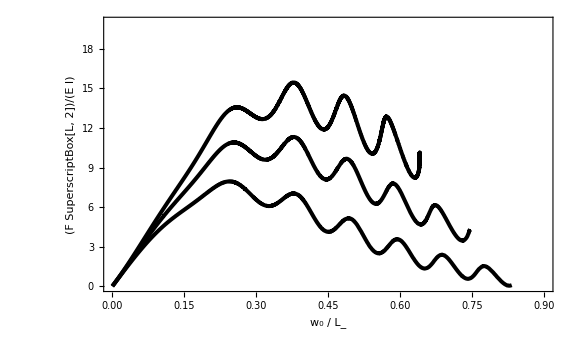

```mathematica
arclength=SolutionVector3[[;;,;;,5]];
frictionC=SolutionVector3[[;;,;;,6]];
levelset=frictionC-1/10 Cos[arclength/0.03];
data1=Flatten[Table[{SolutionVector3[[i,j,1]],SolutionVector3[[i,j,2]],
levelset[[i,j]]},{i,1,Length@SolutionVector3},{j,1,Length[SolutionVector3[[i]]]}],1];
Level0p1=Select[data1,Abs[#[[3]]-0.1]<10^-3&];
Level0p4=Select[data1,Abs[#[[3]]-0.5]<10^-3&];
Level0p8=Select[data1,Abs[#[[3]]-0.8]<10^-3&];
Level0p1S=SortBy[Level0p1,First];
Level0p4S=SortBy[Level0p4,First];
Level0p8S=SortBy[Level0p8,First];
Level3={Level0p1S[[;;,{1,2}]],Level0p4S[[;;,{1,2}]],Level0p8S[[;;,{1,2}]]};
ListPlot[Level3,
Joined->True,
PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,20}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
```

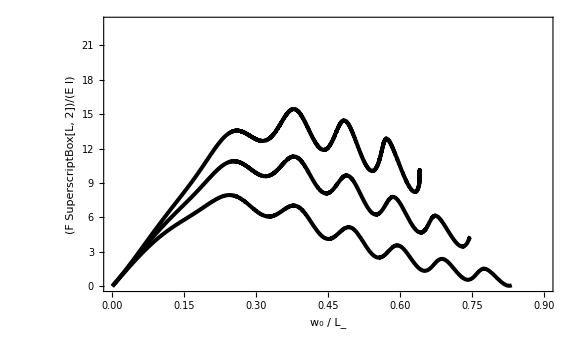

```mathematica
Psinu=ListPlot[Level3,
Joined->True,
PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->{{0.0,0.9},{0,23}},
AxesStyle->Directive[Black,FontFamily->"Times",40],Frame->True,FrameStyle->Directive[Black,Thick,FontFamily->"Times",28],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",28],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",28]},RotateLabel->False,
AspectRatio->0.6]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["SinusoidalFw_V2.eps",Psinu]
```

/Users/wenqiangfang/Dropbox (Personal)/Apps/ShareLaTeX/Stair Step Pattern 2018/Figures

SinusoidalFw_V2.eps

```mathematica
p2=ListContourPlot[data1,
ContourShading->None,
PlotLegends->Automatic,
Contours->{0.1,0.4,0.8},
ImageSize->Large,GridLines->None,Ticks->Automatic,PlotRange->Automatic,
AxesStyle->Directive[Black,FontFamily->"Times",28],Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",16],FrameLabel->{Style["w_0 / L_",Black(*,Italic*),FontFamily->"Times",16],Style["(F SuperscriptBox[L, 2])/(E I)",Black,FontFamily->"Times",16]},RotateLabel->False]
```